```mathematica
Clear[Lx,Ly,A,
sx3d,SX3D,sx3dp,SX3DP,
sy3d,SY3D,sy3dp,SY3DP,
sz3d,SZ3D,sz3dp,SZ3DP,
cx3d,CX3D,cx3dp,CX3DP,
cy3d,CY3D,cy3dp,CY3DP,
cz3d,CZ3D,cz3dp,CZ3DP,
cons,Cons]
```

```mathematica
Lx=16;
Ly=16;
Lz =19;
A=Lx*Ly*Lz;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sx3d[j+k Lx+l Lx Ly,j+1+k Lx + l Lx Ly]=-I/2,sx3d[j+1+k Lx + l Lx Ly,j+k Lx+l Lx Ly]=I/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

SX3D=Table[sx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx3dp[i_Integer,j_Integer]=0;

Do[Do[{sx3dp[(k+1)Lx+ l Lx Ly,1+k Lx+ l Lx Ly]=-I/2,sx3dp[1+k Lx+ l Lx Ly,(k+1)Lx+ l Lx Ly]=I/2},{k,0,Ly-1}],{l,0,Lz-1}]

SX3DP=Table[sx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{sy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=-I/2,sy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

SY3D=Table[sy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy3dp[i_Integer,j_Integer]=0;

Do[Do[{sy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=-I/2,sy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=I/2},{j,1,Lx}],{l,0,Lz-1}]

SY3DP=Table[sy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cx3d[j+k Lx+l Lx Ly,j+1+k Lx+l Lx Ly]=1/2,cx3d[j+1+k Lx+l Lx Ly,j+k Lx+l Lx Ly]=1/2},{j,1,Lx-1}],{k,0,Ly-1}],{l,0,Lz-1}]

CX3D=Table[cx3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx3dp[i_Integer,j_Integer]=0;

Do[Do[{cx3dp[(1+k)Lx+l Lx Ly,1+k Lx+l Lx Ly]=1/2,cx3dp[1+k Lx+l Lx Ly,(1+k)Lx+l Lx Ly]=1/2},{k,0,Ly-1}],{l,0,Lz-1}]

CX3DP=Table[cx3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cy3d[k Lx+j+l Lx Ly,(k+1)Lx+j+l Lx Ly]=1/2,cy3d[(k+1)Lx+j+l Lx Ly,k Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{k,0,Ly-2}],{l,0,Lz-1}]

CY3D=Table[cy3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy3dp[i_Integer,j_Integer]=0;

Do[Do[{cy3dp[(Ly-1)Lx+j+l Lx Ly,j+l Lx Ly]=1/2,cy3dp[j+l Lx Ly,(Ly-1)Lx+j+l Lx Ly]=1/2},{j,1,Lx}],{l,0,Lz-1}]

CY3DP=Table[cy3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cz3d[i_Integer,j_Integer]=0;

Do[Do[Do[{cz3d[j+(k-1) Lx+(l-1) Lx Ly,j+(k-1)Lx+l Lx Ly]=1/2,cz3d[j+(k-1)Lx+l Lx Ly,j+(k-1) Lx+(l-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}],{l,1,Lz-1}]

CZ3D=Table[cz3d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cz3dp[i_Integer,j_Integer]=0;

Do[Do[{cz3dp[(k-1)Lx+j+(Lz-1) Lx Ly,(k-1)Lx+j]=1/2,cz3dp[(k-1)Lx+j,(k-1)Lx+j+(Lz-1) Lx Ly]=1/2},{j,1,Lx}],{k,1,Ly}]

CZ3DP=Table[cz3dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0;

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianWSM[t_,t0_,m_,tz_,αx_,αy_,αz_]:=t*(KroneckerProduct[SX3D+αx*SX3DP,σ1]+KroneckerProduct[SY3D+αy*SY3DP, σ2])+KroneckerProduct[2*Cons-t0*(CX3D+CY3D+αx*CX3DP+αy*CY3DP),σ3]+KroneckerProduct[tz *(CZ3D + αz*CZ3DP)-m*Cons,σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals2D=Dimensions[FlatSite][[1]]
```

128

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals2D,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/3)*(x-1)+4
LineDn[x_]:=(2/3)*(x-2)+2
```

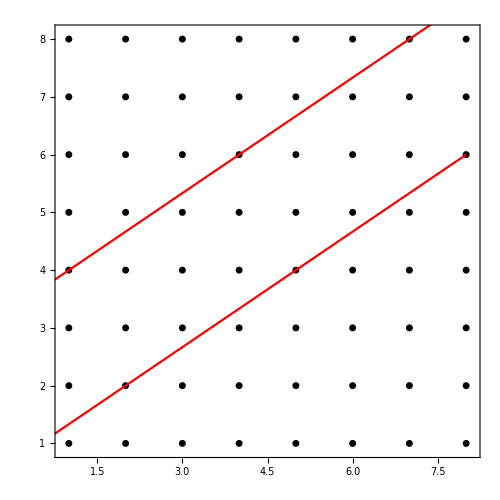

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist2D=Sort[FibonupNew]
```

{9,17,18,19,26,27,28,35,36,37,38,45,46,47,54,55,56,64}

```mathematica
Clear[XList,YList,ZList,zzz1,XList2D,YList2D]
```

```mathematica
XList2D =Mod[Fibonlist2D,Lx,1]
```

{1,1,2,3,2,3,4,3,4,5,6,5,6,7,6,7,8,8}

```mathematica
YList2D =Ceiling[Fibonlist2D/Lx]
```

{2,3,3,3,4,4,4,5,5,5,5,6,6,6,7,7,7,8}

```mathematica
Dimensions[XList2D]
```

{18}

```mathematica
XList = {};
YList={};
ZList = {};
```

```mathematica
Do[XList = Append[XList,XList2D ],{n,1,Lz}]
```

```mathematica
XList = Flatten[XList];
```

```mathematica
Do[YList = Append[YList,YList2D ],{n,1,Lz}]
```

```mathematica
YList = Flatten[YList];
```

```mathematica
zzz1 = Table[1,{n,1,Dimensions[XList2D][[1]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Do[ZList = Append[ZList,zzz1 * m],{m,1,Lz}]
```

```mathematica
ZList = Flatten[ZList];
```

```mathematica
Fibonlist={};
```

```mathematica
Do[Fibonlist = Append[Fibonlist,Fibonlist2D+n*Lx*Ly],{n,0,Lz-1}];
```

```mathematica
Fibonlist;
```

```mathematica
Fibonlist=Sort[Flatten[Fibonlist]];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

288

```mathematica
NOrbitalsQuasi/2
```

144

```mathematica
NOrbitalsQuasi2D = NOrbitalsQuasi/Lz
```

36

```mathematica
NOrbitalsOutside = NOrbitals2D*Lz-NOrbitalsQuasi
```

736

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.28125

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{1024}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianWSM[1.,1.,0,1,0,0,0];
```

```mathematica
Dimensions[HTrial]
```

{1024,1024}

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D] (** To save memory **)
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

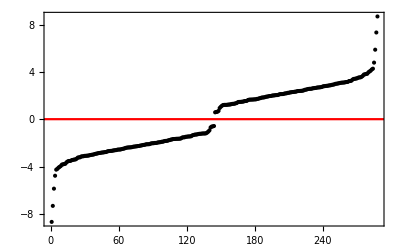

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black(**,PlotRange->{{0,84},{-2,2}}**)],Plot[0,{x,-10,NOrbitalsQuasi+10},PlotStyle-> Red]]
```

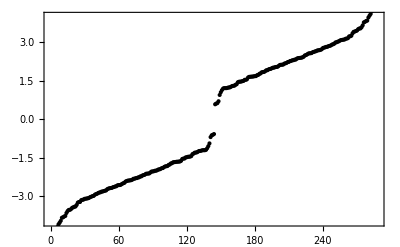

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{All,{-4,4}}]]
```

```mathematica
Clear[datDensity,MidEigvec1, MidEigvec2]
```

```mathematica
MidEigvec1 = ValVecFibon[[NOrbitalsQuasi/2]][[2]] ;
```

```mathematica
MidEigvec2 = ValVecFibon[[NOrbitalsQuasi/2 + 1]][[2]];
```

```mathematica
datDensity = Table[{XList[[m]],YList[[m]],ZList[[m]],(Abs[MidEigvec1[[2*m]]]^2 + Abs[MidEigvec1[[2*m-1]]]^2 + Abs[MidEigvec2[[2*m]]]^2 + Abs[MidEigvec2[[2*m-1]]]^2)/2 },{m,1,NOrbitalsQuasi/2}];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@datDensity[[All,4]];
```

```mathematica
rng[[2]]
```

0.0747001

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.0165"},{rng[[2]]-10^-4,"0.033"}}]
```

```mathematica
Graphics3D[{PointSize[0.020],colorfunc[#[[4]],rng[[2]]],Point[#[[1;;3]]]}&/@datDensity,Axes->True,BoxRatios->1,BoxStyle->Directive[Thickness[0.0075]],AxesLabel->{"x","y","z"},BaseStyle->15,Ticks-> {{{1,"1"},{16,"16"}},{{1,"1"},{16,"16"}},{{1,"1"},{19,"19"}}},PlotRange->{{1,Lx},{1,Ly},{1,Lz}},ImageSize->400]
```

-Graphics3D-

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi2D/2-1}]
```

{{1.,0},{1.9245,0},{2.4792,0},{3.4037,0},{4.3282,0},{4.8829,0},{5.8074,0},{6.7319,0},{7.2866,0},{8.2111,0},{9.1356,0},{9.6903,0},{10.6148,0},{11.5393,0},{12.094,0},{13.0185,0},{13.943,0},{14.4977,0}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

15

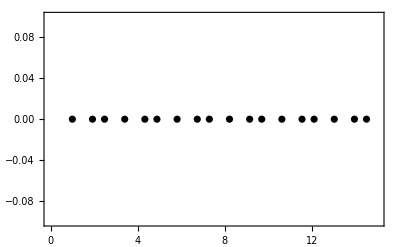

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black,PlotStyle->Small]
```

```mathematica
Fibon1D[[3,1]]
```

2.4792

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon={};
```

```mathematica
ValVecFibon[[1,1]]
```

-8.68125+8.09005×10^-16 ⅈ

```mathematica
Do[Do[TabDataFibon=Append[TabDataFibon,{Mod[i,NOrbitalsQuasi2D/2,1],z,
(Abs[ValVecFibon[[J,2,2i]]]^2+Abs[ValVecFibon[[J,2,2i-1]]]^2

+Abs[ValVecFibon[[J+1,2,2i]]]^2+Abs[ValVecFibon[[J+1,2,2i-1]]]^2)/2

}],{i,1+(z-1)*NOrbitalsQuasi2D/2,NOrbitalsQuasi2D/2+(z-1)*NOrbitalsQuasi2D/2}],{z,1,Lz}];
```

```mathematica
Dimensions[TabDataFibon]
```

{144,3}

```mathematica
TabDataFibon;
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
(** Divide the last term by 2 for normalization **)
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]/2},{i,1,3*NOrbitalsQuasi/2,3}]
```

{{1,1,0.00288382},{2,1,0.00264968},{3,1,0.0000392831},{4,1,4.13963×10^-6},{5,1,0.0000328949},{6,1,5.18491×10^-6},{7,1,8.58016×10^-7},{8,1,1.53775×10^-7},{9,1,4.03142×10^-8},{10,1,3.37514×10^-8},{11,1,1.93866×10^-7},{12,1,1.0187×10^-6},{13,1,3.3608×10^-6},{14,1,0.0000185775},{15,1,0.0000295516},{16,1,0.0000867476},{17,1,0.00273702},{18,1,0.00450497},{1,2,0.0101859},{2,2,0.0093589},{3,2,0.000138751},{4,2,0.0000146215},{5,2,0.000116188},{6,2,0.0000183136},{7,2,3.03059×10^-6},{8,2,5.43148×10^-7},{9,2,1.42393×10^-7},{10,2,1.19213×10^-7},{11,2,6.84752×10^-7},{12,2,3.59814×10^-6},{13,2,0.0000118706},{14,2,0.0000656172},{15,2,0.000104379},{16,2,0.0003064},{17,2,0.0096674},{18,2,0.0159119},{1,3,0.0184896},{2,3,0.0169883},{3,3,0.000251863},{4,3,0.0000265411},{5,3,0.000210905},{6,3,0.0000332429},{7,3,5.50115×10^-6},{8,3,9.85926×10^-7},{9,3,2.58473×10^-7},{10,3,2.16396×10^-7},{11,3,1.24297×10^-6},{12,3,6.53137×10^-6},{13,3,0.0000215477},{14,3,0.000119109},{15,3,0.000189469},{16,3,0.00055618},{17,3,0.0175483},{18,3,0.0288835},{1,4,0.0239094},{2,4,0.0219681},{3,4,0.000325691},{4,4,0.000034321},{5,4,0.000272727},{6,4,0.0000429873},{7,4,7.11369×10^-6},{8,4,1.27493×10^-6},{9,4,3.34239×10^-7},{10,4,2.79828×10^-7},{11,4,1.60732×10^-6},{12,4,8.4459×10^-6},{13,4,0.0000278639},{14,4,0.000154023},{15,4,0.000245008},{16,4,0.000719212},{17,4,0.0226923},{18,4,0.0373501},{1,5,0.0239094},{2,5,0.0219681},{3,5,0.000325691},{4,5,0.000034321},{5,5,0.000272727},{6,5,0.0000429873},{7,5,7.11369×10^-6},{8,5,1.27493×10^-6},{9,5,3.34239×10^-7},{10,5,2.79828×10^-7},{11,5,1.60732×10^-6},{12,5,8.4459×10^-6},{13,5,0.0000278639},{14,5,0.000154023},{15,5,0.000245008},{16,5,0.000719212},{17,5,0.0226923},{18,5,0.0373501},{1,6,0.0184896},{2,6,0.0169883},{3,6,0.000251863},{4,6,0.0000265411},{5,6,0.000210905},{6,6,0.0000332429},{7,6,5.50115×10^-6},{8,6,9.85926×10^-7},{9,6,2.58473×10^-7},{10,6,2.16396×10^-7},{11,6,1.24297×10^-6},{12,6,6.53137×10^-6},{13,6,0.0000215477},{14,6,0.000119109},{15,6,0.000189469},{16,6,0.00055618},{17,6,0.0175483},{18,6,0.0288835},{1,7,0.0101859},{2,7,0.0093589},{3,7,0.000138751},{4,7,0.0000146215},{5,7,0.000116188},{6,7,0.0000183136},{7,7,3.03059×10^-6},{8,7,5.43148×10^-7},{9,7,1.42393×10^-7},{10,7,1.19213×10^-7},{11,7,6.84752×10^-7},{12,7,3.59814×10^-6},{13,7,0.0000118706},{14,7,0.0000656172},{15,7,0.000104379},{16,7,0.0003064},{17,7,0.0096674},{18,7,0.0159119},{1,8,0.00288382},{2,8,0.00264968},{3,8,0.0000392831},{4,8,4.13963×10^-6},{5,8,0.0000328949},{6,8,5.18491×10^-6},{7,8,8.58016×10^-7},{8,8,1.53775×10^-7},{9,8,4.03142×10^-8},{10,8,3.37514×10^-8},{11,8,1.93866×10^-7},{12,8,1.0187×10^-6},{13,8,3.3608×10^-6},{14,8,0.0000185775},{15,8,0.0000295516},{16,8,0.0000867476},{17,8,0.00273702},{18,8,0.00450497}}

```mathematica
Clear[rng,P1]
```

```mathematica
rngOld={0,Max[#]}&@(TabFibonacci[[All,3]])
```

{0,0.0373501}

```mathematica
rng = rngOld
```

{0,0.0373501}

```mathematica
rng={0,0.018284585223185105}
```

{0,0.0182846}

```mathematica
rng[[2]]
```

0.0182846

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"9.15x10^-3"},{rng[[2]]-0.2*10^-3,"1.83x10^-2"}}]
```

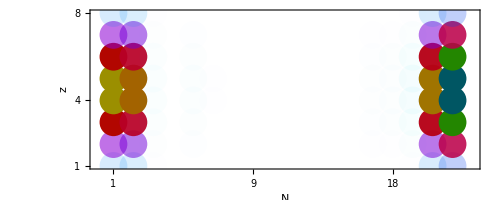

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
BaseStyle-> 18,
PlotRange-> {{0.2,largestX+4},{1,Lz}}],
FrameTicks->{{{1,Ceiling[Lz/2],Lz},None},{{1,{Ceiling[largestX/2],Ceiling[NOrbitalsQuasi2D/4]},{largestX,NOrbitalsQuasi2D/2}},None}},FrameLabel-> {"N","z"},RotateLabel-> False
]
```

```mathematica
(** Export["dataFermiArcReal_Rational_3D_Up+6_Dn+4.dat",TabFibonacci]; **)
```